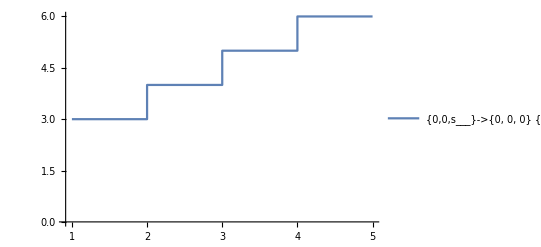
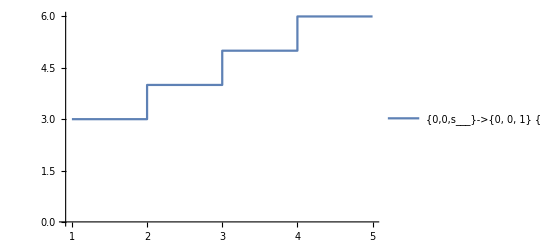
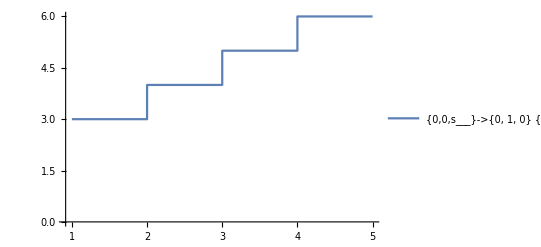
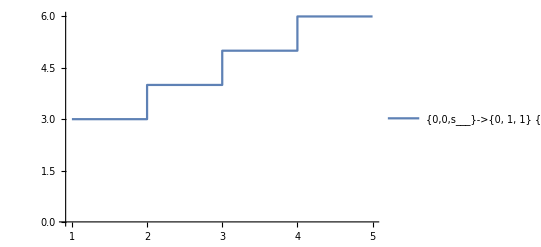
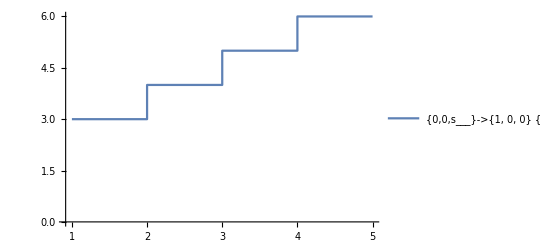
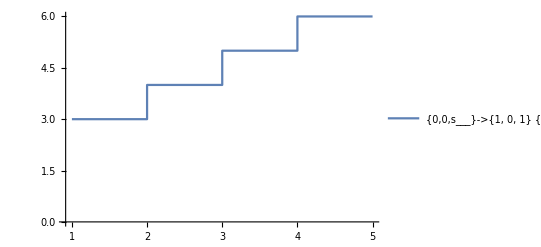
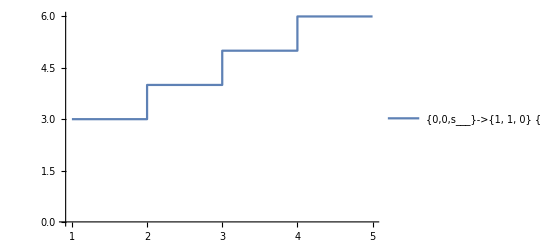
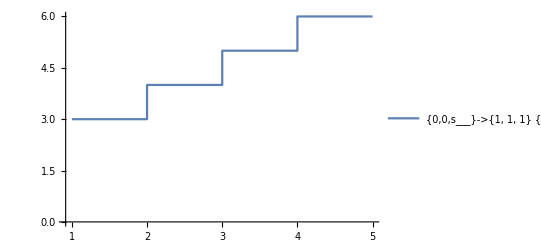

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},2]
},
Length /@FindShortestPath[g,First[VertexList[g]],vertices[[Length[vertices]]]]
]//.{x_}:>x]]

lFn[i1_,i2_,i3_,i4_,j_,k_,l_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]}],{Tuples[{0,1},l][[k]]},t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]

Table[Table[Table[Table[Table[Show[
ListStepPlot[
Legended[
lFn[i1,i2,i3,i4,j,k,l,t][[1]][[1]],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]
|>]
]]],{t,3,3}],
{i1,1,2^j},
{i2,2^(j-1),2^(j-1)},
{i3,2^(j-2),2^(j-2)},
{i4,2^(j-2),2^(j-2)}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]
```